```mathematica
problem = Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/coax_cyl/problem1.dat"]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},10030,{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{}}
 |  |  |  |

```mathematica
problem1 = ArrayReshape[problem, {100,100}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.1247,0.249405,0.374114,0.49881,0.623458,0.747999,0.872342,0.996359,1.11988,1.24267,1.36445,1.48487,1.6035,1.71982,1.83323,1.94301,2.04837,2.14839,2.24211,2.32849,2.40653,2.47528,2.53397,2.58209,2.61949,2.64646,2.66379,2.67282,2.67537,2.67371,2.67049,2.66864,2.67125,2.68152,2.7027,2.73797,2.79044,2.86303,2.95834,3.07847,3.22467,3.3969,3.59316,3.80872,4.03524,4.2602,4.46685,4.63555,4.74675,4.78558,4.74636,4.63476,4.46567,4.25862,4.03325,3.80631,3.59033,3.39363,3.22093,3.07424,2.95359,2.85771,2.78452,2.73138,2.69538,2.67341,2.66225,2.65867,2.65944,2.66145,2.66176,2.65773,2.64705,2.6279,2.59893,2.55935,2.50886,2.4476,2.37608,2.29508,2.20553,2.10845,2.00486,1.89574,1.782,1.66444,1.54377,1.42061,1.29546,1.16878,1.0409,0.91213,0.782697,0.652788,0.522543,0.392071,0.261453,0.130747,0},{0,0.249405,0.498829,0.748271,0.997705,1.24707,1.49625,1.74507,1.99329,2.24055,2.48643,2.73035,2.97162,3.2094,3.44266,3.67018,3.89057,4.10218,4.30322,4.49167,4.66546,4.82247,4.96075,5.07864,5.17504,5.24954,5.30268,5.33604,5.35227,5.35509,5.34913,5.33977,5.33296,5.33498,5.3523,5.39146,5.4589,5.56092,5.70349,5.89202,6.13102,6.42346,6.76991,7.16716,7.60659,8.07218,8.53883,8.97177,9.32871,9.56601,9.6493,9.56522,9.32713,8.96941,8.53567,8.06821,7.6018,7.16152,6.76338,6.41601,6.12258,5.88254,5.69289,5.54911,5.44578,5.37689,5.33615,5.31708,5.31311,5.31777,5.32472,5.32801,5.32222,5.30271,5.26572,5.20859,5.12973,5.02859,4.90556,4.76175,4.5988,4.41868,4.2235,4.01534,3.7962,3.56789,3.33206,3.09011,2.84326,2.59253,2.33879,2.08275,1.82497,1.56591,1.30594,1.04534,0.784308,0.523005,0.26154,0},{0,0.374114,0.748271,1.12249,1.49673,1.87094,2.24495,2.61852,2.99128,3.36275,3.73228,4.09905,4.46203,4.81999,5.17139,5.51446,5.84707,6.16678,6.47081,6.7561,7.0194,7.25735,7.46681,7.64504,7.7901,7.90118,7.97893,8.02564,8.04537,8.04383,8.02818,8.00676,7.98871,7.98366,8.00151,8.05218,8.14551,8.29112,8.49824,8.77548,9.13036,9.5685,10.0923,10.6992,11.3785,12.1083,12.8514,13.5529,14.1417,14.5394,14.6806,14.5383,14.1393,13.5494,12.8466,12.1024,11.3714,10.6908,10.0826,9.55737,9.11777,8.76134,8.48244,8.27352,8.12596,8.03049,7.97746,7.95702,7.95918,7.97403,7.99187,8.00354,8.00066,7.97603,7.9239,7.84019,7.72257,7.5704,7.38447,7.16672,6.91986,6.64707,6.35168,6.03695,5.70595,5.36146,5.00593,4.64147,4.26989,3.89272,3.51122,3.12641,2.73915,2.3501,1.95978,1.5686,1.17685,0.784735,0.392416,0},{0,0.49881,0.997705,1.49673,1.9959,2.49512,2.99422,3.49291,3.99073,4.48706,4.98108,5.47173,5.95769,6.43734,6.90871,7.36944,7.81673,8.2473,8.65741,9.04282,9.39895,9.72103,10.0044,10.2449,10.4394,10.5865,10.6865,10.7426,10.7601,10.747,10.7134,10.6707,10.6318,10.6098,10.6182,10.6706,10.7802,10.9602,11.2232,11.5816,12.0468,12.6282,13.3321,14.1591,15.1003,16.1313,17.2057,18.247,19.146,19.7697,19.9956,19.7682,19.1428,18.2423,17.1994,16.1235,15.0908,14.148,13.3192,12.6134,12.0301,11.563,11.2023,10.9369,10.7544,10.642,10.5865,10.5747,10.5929,10.6276,10.6655,10.6939,10.7011,10.6771,10.6139,10.5059,10.3502,10.1462,9.89546,9.60103,9.26709,8.89829,8.49941,8.07503,7.62939,7.16625,6.68889,6.20011,5.70228,5.19739,4.68706,4.17265,3.65522,3.13564,2.61456,2.09249,1.56979,1.0467,0.523397,0},{0,0.623458,1.24707,1.87094,2.49512,3.11955,3.74407,4.36834,4.99186,5.6139,6.23349,6.84936,7.45994,8.06327,8.65697,9.23817,9.80342,10.3486,10.869,11.3592,11.8129,12.2238,12.5852,12.8911,13.1367,13.3191,13.4385,13.4984,13.5058,13.4712,13.4079,13.3315,13.2584,13.206,13.1915,13.2322,13.345,13.5465,13.8533,14.2816,14.8474,15.5657,16.4491,17.5053,18.7325,20.1115,21.5934,23.0838,24.4257,25.3983,25.764,25.3964,24.4218,23.078,21.5856,20.1017,18.7208,17.4915,16.4331,15.5475,14.8268,14.2584,13.8274,13.5178,13.3131,13.1969,13.1524,13.1627,13.2105,13.2784,13.3491,13.4058,13.4332,13.4178,13.349,13.2198,13.0265,12.7691,12.4504,12.0752,11.6495,11.1799,10.6729,10.1346,9.57058,8.98551,8.3835,7.76801,7.14193,6.50766,5.86716,5.22204,4.57357,3.92278,3.27043,2.61709,1.96316,1.3089,0.654486,0},{0,0.747999,1.49625,2.24495,2.99422,3.74407,4.49436,5.24476,5.99473,6.74347,7.4899,8.23259,8.96975,9.69917,10.4181,11.1232,11.8105,12.4752,13.1114,13.7123,14.2702,14.7764,15.222,15.5981,15.8975,16.1153,16.2506,16.3072,16.2939,16.2245,16.1163,15.9893,15.8649,15.7647,15.7102,15.7223,15.8216,16.0282,16.3623,16.8445,17.496,18.3386,19.3938,20.6811,22.2135,23.989,25.9731,28.0695,30.0751,31.6342,32.2662,31.6319,30.0704,28.0626,25.9638,23.9774,22.1996,20.6647,19.3748,18.317,17.4716,16.8171,16.3317,15.9942,15.784,15.6806,15.664,15.7136,15.8084,15.9268,16.047,16.1476,16.2085,16.2123,16.1451,15.998,15.7673,15.4538,15.0622,14.6001,14.0761,13.4992,12.878,12.2204,11.5331,10.822,10.0918,9.34675,8.59001,7.82437,7.05208,6.27494,5.49441,4.71161,3.92739,3.14235,2.35691,1.57131,0.785657,0},{0,0.872342,1.74507,2.61852,3.49291,4.36834,5.24476,6.12186,6.99911,7.87567,8.75038,9.62171,10.4877,11.3459,12.1934,13.0266,13.8408,14.6306,15.3894,16.109,16.7796,17.3903,17.9286,18.3824,18.7404,18.9945,19.1419,19.1864,19.1389,19.0171,18.844,18.6452,18.4477,18.2783,18.1628,18.126,18.1916,18.383,18.7238,19.2387,19.9542,20.8995,22.1069,23.6122,25.4521,27.6583,30.2408,33.1466,36.1712,38.7975,40.0351,38.7948,36.1659,33.1386,30.2302,27.645,25.436,23.5933,22.0851,20.8746,19.9261,19.2072,18.6887,18.344,18.1484,18.0782,18.1101,18.22,18.3833,18.5739,18.765,18.9295,19.0415,19.0781,19.0215,18.8604,18.5913,18.2168,17.7451,17.1874,16.556,15.8631,15.1199,14.3361,13.5198,12.6778,11.8155,10.9374,10.0473,9.14799,8.24206,7.33144,6.41769,5.50201,4.58529,3.66813,2.7509,1.8338,0.916852,0},{0,0.996359,1.99329,2.99128,3.99073,4.99186,5.99473,6.99911,8.00451,9.01008,10.0146,11.0166,12.0139,13.0039,13.9837,14.9492,15.8959,16.8177,17.7072,18.5551,19.3497,20.0769,20.7205,21.263,21.6877,21.9811,22.1369,22.1581,22.0586,21.8619,21.598,21.3005,21.0031,20.7386,20.5375,20.4278,20.4364,20.5891,20.912,21.433,22.1832,23.1988,24.523,26.2094,28.3248,30.952,34.1857,38.1054,42.6661,47.35,50.2821,47.3469,42.6601,38.0964,34.1737,30.937,28.3067,26.1881,24.4984,23.1708,22.1517,21.3977,20.8726,20.5454,20.3881,20.3745,20.4786,20.6737,20.9314,21.2212,21.5103,21.7646,21.9505,22.0377,22.0027,21.8316,21.521,21.0776,20.5146,19.8488,19.0978,18.2778,17.4029,16.4847,15.5327,14.5542,13.5552,12.5405,11.5139,10.4786,9.437,8.39131,7.34311,6.29363,5.24377,4.19407,3.14485,2.09618,1.04797,0},{0,1.11988,2.24055,3.36275,4.48706,5.6139,6.74347,7.87567,9.01008,10.1459,11.2819,12.4165,13.5477,14.6727,15.7886,16.8914,17.9764,19.0376,20.0673,21.0551,21.9877,22.8477,23.614,24.2622,24.7668,25.106,25.2671,25.2512,25.0764,24.7745,24.3865,23.9562,23.5265,23.1365,22.8213,22.6123,22.538,22.6257,22.9028,23.3989,24.1478,25.1902,26.5775,28.3781,30.6865,33.6397,37.4453,42.4237,49.0383,57.6545,66.3969,57.6511,49.0316,42.4137,37.432,33.6231,30.6665,28.3546,26.5504,25.1593,24.113,23.3599,22.8594,22.5776,22.4849,22.5537,22.7568,23.0654,23.4482,23.8698,24.291,24.6686,24.9587,25.1201,25.1208,24.9426,24.5842,24.0584,23.3872,22.596,21.7091,20.7478,19.7295,18.6676,17.5724,16.4515,15.3111,14.1559,12.9897,11.8156,10.6363,9.45393,8.27002,7.08584,5.90223,4.71967,3.53834,2.35816,1.17885,0},{0,1.24267,2.48643,3.73228,4.98108,6.23349,7.4899,8.75038,10.0146,11.2819,12.5511,13.8205,15.0881,16.3513,17.6071,18.8519,20.0813,21.2897,22.4697,23.611,24.6988,25.713,26.6265,27.4054,28.0119,28.4099,28.5748,28.504,28.2218,27.7741,27.218,26.6123,26.0108,25.4603,24.9999,24.663,24.4785,24.4737,24.6754,25.1128,25.8197,26.8374,28.2196,30.0398,32.404,35.4758,39.5325,45.1064,53.4095,67.833,100,67.8293,53.4021,45.0955,39.518,35.4577,32.3822,30.0142,28.1901,26.8037,25.7817,25.0704,24.6282,24.4215,24.4209,24.5996,24.9303,25.3838,25.9267,26.5197,27.1158,27.661,28.0962,28.364,28.4182,28.2344,27.8153,27.1853,26.3806,25.4393,24.3952,23.2754,22.1003,20.8844,19.6381,18.3688,17.0822,15.7826,14.4736,13.1583,11.8391,10.5183,9.19743,7.87768,6.55981,5.24418,3.93079,2.61933,1.3093,0},{0,1.36445,2.73035,4.09905,5.47173,6.84936,8.23259,9.62171,11.0166,12.4165,13.8205,15.2268,16.6334,18.0379,19.4372,20.8284,22.2078,23.5709,24.9117,26.2209,27.4843,28.6797,29.7741,30.7219,31.4664,31.9475,32.119,31.9691,31.5336,30.8827,30.0999,29.2649,28.4452,27.6948,27.056,26.5619,26.2404,26.116,26.2132,26.5583,27.1816,28.1209,29.4246,31.1585,33.4146,36.3277,40.1033,45.0604,51.6606,60.2684,69.0079,60.2645,51.6528,45.0487,40.0878,36.3082,33.3911,31.1309,29.3928,28.0846,27.1408,26.5126,26.1625,26.06,26.1787,26.4942,26.9817,27.6135,28.3561,29.1671,29.9924,30.764,31.4018,31.8221,31.9542,31.7623,31.2578,30.4874,29.5112,28.386,27.1576,25.859,24.5124,23.1321,21.7273,20.304,18.8668,17.4191,15.9643,14.5051,13.044,11.5831,10.124,8.66786,7.21533,5.76659,4.32139,2.87915,1.43903,0},{0,1.48487,2.97162,4.46203,5.95769,7.45994,8.96975,10.4877,12.0139,13.5477,15.0881,16.6334,18.1816,19.7301,21.2762,22.8174,24.3513,25.8752,27.3858,28.8774,30.3385,31.7481,33.069,34.2425,35.1848,35.7957,35.9852,35.7206,35.0615,34.1241,33.0351,31.9031,30.8111,29.8188,28.9682,28.2894,27.8059,27.5377,27.5042,27.7264,28.2286,29.0407,30.2004,31.7558,33.7689,36.3179,39.4935,43.3718,47.9048,52.5727,55.4993,52.5686,47.8965,43.3594,39.477,36.2971,33.7439,31.7264,30.1664,29.0021,28.185,27.6777,27.4502,27.4781,27.7404,28.2177,28.8898,29.7333,30.7178,31.8012,32.9235,34.0014,34.9256,35.5692,35.815,35.6033,34.9669,33.996,32.7913,31.4365,29.9907,28.491,26.9587,25.4049,23.8354,22.2537,20.6622,19.0633,17.4598,15.8542,14.249,12.6463,11.0479,9.45467,7.86728,6.28562,4.70914,3.13692,1.56769,0},{0,1.6035,3.2094,4.81999,6.43734,8.06327,9.69917,11.3459,13.0039,14.6727,16.3513,18.0379,19.7301,21.4252,23.1208,24.8145,26.5054,28.1935,29.8799,31.565,33.245,34.9058,36.5123,37.9949,39.2355,40.066,40.3062,39.8676,38.8683,37.5181,36.014,34.5021,33.0783,31.8022,30.7095,29.8227,29.1573,28.7258,28.5406,28.6154,28.9667,29.6141,30.5815,31.8964,33.5883,35.6822,38.1819,41.0292,44.015,46.619,47.8488,46.6146,44.0063,41.0161,38.1645,35.6603,33.5618,31.8652,30.5455,29.5731,28.9205,28.5639,28.4835,28.6629,29.0882,29.7473,30.6274,31.7129,32.9815,34.397,35.8997,37.3933,38.7309,39.7146,40.1338,39.8697,39.0112,37.7391,36.222,34.5785,32.8783,31.1564,29.427,27.6939,25.9564,24.2137,22.4654,20.7127,18.9578,17.2033,15.4518,13.7057,11.9667,10.236,8.5137,6.79961,5.09277,3.39176,1.69484,0},{0,1.71982,3.44266,5.17139,6.90871,8.65697,10.4181,12.1934,13.9837,15.7886,17.6071,19.4372,21.2762,23.1208,24.9678,26.8152,28.6629,30.5142,32.3759,34.2583,36.1716,38.1186,40.0801,41.99,43.6969,44.9274,45.3068,44.576,43.0269,41.0669,39.0017,37.0138,35.199,33.603,32.2459,31.1356,30.2757,29.6686,29.318,29.2292,29.4096,29.8685,30.616,31.661,33.0067,34.6418,36.5237,38.5488,40.5077,42.0403,42.6631,42.0358,40.4986,38.5351,36.5054,34.6188,32.9789,31.6282,30.5782,29.8254,29.3611,29.175,29.258,29.6026,30.2034,31.0568,32.1604,33.5105,35.0992,36.9064,38.886,40.9419,42.8906,44.4252,45.1365,44.7313,43.4697,41.7277,39.7799,37.7779,35.7882,33.8298,31.8998,29.9877,28.0834,26.1797,24.2735,22.3649,20.4559,18.5497,16.6496,14.7583,12.8777,11.009,9.15218,7.30654,5.47067,3.64259,1.81992,0},{0,1.83323,3.67018,5.51446,7.36944,9.23817,11.1232,13.0266,14.9492,16.8914,18.8519,20.8284,22.8174,24.8145,26.8152,28.8163,30.8178,32.8252,34.8521,36.9216,39.0652,41.3175,43.7005,46.1888,48.6356,50.6405,51.4184,50.1033,47.5973,44.7218,41.9131,39.3535,37.1018,35.1661,33.5365,32.1993,31.1423,30.3561,29.8346,29.5747,29.5751,29.8354,30.3541,31.1259,32.1366,33.3555,34.7232,36.1356,37.4276,38.3724,38.7283,38.3677,37.4182,36.1214,34.7042,33.3315,32.1076,31.0917,30.3146,29.7904,29.5244,29.5181,29.7719,30.2871,31.0668,32.1172,33.4477,35.0705,36.9994,39.2442,41.7969,44.5983,47.4653,49.9596,51.2565,50.4498,48.4092,45.9228,43.3926,40.9657,38.6675,36.4756,34.3552,32.2744,30.2102,28.1488,26.0846,24.0178,21.9516,19.8906,17.839,15.8005,13.7773,11.7704,9.77969,7.80388,5.84092,3.8881,1.94227,0},{0,1.94301,3.89057,5.84707,7.81673,9.80342,11.8105,13.8408,15.8959,17.9764,20.0813,22.2078,24.3513,26.5054,28.6629,30.8178,32.9674,35.1175,37.2865,39.5114,41.8509,44.3864,47.2162,50.4298,54.0167,57.5812,59.6236,56.8222,52.5381,48.3107,44.5763,41.3861,38.6897,36.4241,34.5357,32.984,31.7391,30.7799,30.0909,29.6611,29.4819,29.5449,29.8401,30.3529,31.0594,31.9214,32.879,33.8437,34.6958,35.2942,35.5111,35.2894,34.686,33.8291,32.8594,31.8966,31.0294,30.3175,29.7991,29.4981,29.4292,29.6022,30.0256,30.708,31.6606,32.8987,34.4436,36.3253,38.5845,41.2749,44.4598,48.1898,52.4133,56.6922,59.4804,57.4029,53.7949,50.1625,46.9025,44.0254,41.441,39.0504,36.7715,34.5453,32.3347,30.1211,27.8989,25.6707,23.4428,21.2223,19.0158,16.8277,14.6608,12.516,10.3925,8.28856,6.20115,4.12669,2.0611,0},{0,2.04837,4.10218,6.16678,8.2473,10.3486,12.4752,14.6306,16.8177,19.0376,21.2897,23.5709,25.8752,28.1935,30.5142,32.8252,35.1175,37.3915,39.6659,41.9875,44.4414,47.1617,50.3488,54.2983,59.421,66.0446,72.6731,65.0246,57.4229,51.4076,46.6962,42.9258,39.848,37.3059,35.1995,33.4629,32.0516,30.9345,30.0891,29.4982,29.1475,29.0233,29.1098,29.3872,29.8277,30.3928,31.0288,31.6656,32.2185,32.5986,32.7334,32.5936,32.2085,31.6506,31.0086,30.3673,29.7968,29.3506,29.0675,28.9749,29.0929,29.4371,30.0213,30.8599,31.97,33.3742,35.1039,37.2035,39.7394,42.8118,46.5785,51.2885,57.3065,64.9159,72.5707,65.8867,59.2059,54.0302,50.0301,46.793,44.0215,41.5141,39.1358,36.8011,34.4629,32.1026,29.7199,27.3238,24.9269,22.5408,20.1745,17.8341,15.5225,13.2404,10.9862,8.75688,6.54857,4.35649,2.17546,0},{0,2.14839,4.30322,6.47081,8.65741,10.869,13.1114,15.3894,17.7072,20.0673,22.4697,24.9117,27.3858,29.8799,32.3759,34.8521,37.2865,39.6659,41.9988,44.3321,46.7663,49.471,52.7196,56.9942,63.3248,74.5035,100,73.1805,60.7222,53.2012,47.8763,43.7738,40.4715,37.7532,35.4945,33.6176,32.071,30.8185,29.8338,29.0962,28.5879,28.292,28.1898,28.2593,28.4727,28.7942,29.1788,29.5724,29.9151,30.1493,30.2312,30.1443,29.905,29.557,29.1582,28.7682,28.4411,28.2219,28.1463,28.2422,28.5317,29.0331,29.7637,30.7412,31.9863,33.5255,35.395,37.6466,40.3585,43.6555,47.7545,53.0799,60.609,73.0946,100,74.368,63.1122,56.7228,52.3955,49.0957,46.3386,43.8494,41.4572,39.0611,36.6139,34.1072,31.5546,28.9784,26.4008,23.8398,21.3078,18.812,16.3553,13.9372,11.5551,9.20444,6.87989,4.57533,2.28427,0},{0,2.24211,4.49167,6.7561,9.04282,11.3592,13.7123,16.109,18.5551,21.0551,23.611,26.2209,28.8774,31.565,34.2583,36.9216,39.5114,41.9875,44.3321,46.5766,48.8215,51.2372,54.065,57.6349,62.381,68.6449,74.9368,66.976,59.0849,52.7997,47.8347,43.8228,40.512,37.7419,35.4088,33.4433,31.7973,30.4359,29.3326,28.466,27.8172,27.368,27.0991,26.9887,27.0107,27.1336,27.3208,27.5309,27.7214,27.8533,27.899,27.8482,27.7111,27.5155,27.2999,27.1072,26.9785,26.9506,27.0548,27.317,27.7594,28.4011,29.2603,30.356,31.7095,33.3475,35.3051,37.6305,40.3934,43.6979,47.7051,52.6681,58.9554,66.8539,74.8207,68.4735,62.1526,57.3539,53.7339,50.8562,48.3885,46.0882,43.7833,41.3726,38.8249,36.1582,33.4136,30.6349,27.8586,25.1102,22.4053,19.7512,17.1497,14.5985,12.0927,9.62611,7.19136,4.78075,2.38633,0},{0,2.32849,4.66546,7.0194,9.39895,11.8129,14.2702,16.7796,19.3497,21.9877,24.6988,27.4843,30.3385,33.245,36.1716,39.0652,41.8509,44.4414,46.7663,48.8215,50.7066,52.5921,54.6692,57.0998,59.92,62.759,64.1268,60.7025,55.8424,51.0791,46.841,43.1716,40.0129,37.2947,34.9565,32.9506,31.2402,29.7964,28.596,27.6191,26.8479,26.2647,25.8512,25.5869,25.4486,25.4098,25.4409,25.5103,25.5871,25.6446,25.6642,25.6395,25.5768,25.4947,25.4199,25.3833,25.4162,25.5483,25.8061,26.2129,26.7889,27.5526,28.5217,29.7139,31.1492,32.851,34.8482,37.1778,39.8876,43.0384,46.7008,50.9329,55.6912,60.5452,63.9561,62.5532,59.6715,56.8068,54.3309,52.2071,50.2719,48.3321,46.2156,43.8219,41.1555,38.2877,35.3071,32.2897,29.289,26.3377,23.4523,20.6383,17.8943,15.2146,12.5916,10.0161,7.47882,4.97009,2.48032,0},{0,2.40653,4.82247,7.25735,9.72103,12.2238,14.7764,17.3903,20.0769,22.8477,25.713,28.6797,31.7481,34.9058,38.1186,41.3175,44.3864,47.1617,49.471,51.2372,52.5921,53.7562,54.9206,56.176,57.441,58.3448,58.1098,55.8656,52.504,48.8341,45.2796,42.0106,39.0745,36.4687,34.173,32.1635,30.4175,28.9146,27.6369,26.5677,25.6916,24.9928,24.455,24.0601,23.7882,23.6173,23.5236,23.4832,23.4732,23.4746,23.4749,23.4696,23.463,23.4678,23.5028,23.5907,23.7557,24.0214,24.4097,24.9405,25.6317,26.5,27.5608,28.8299,30.3236,32.0602,34.06,36.3459,38.9419,41.8682,45.1275,48.6724,52.3318,55.6804,57.9058,58.1123,57.174,55.8714,54.5765,53.3702,52.1604,50.7533,48.9258,46.5447,43.688,40.5305,37.2381,33.9282,30.6706,27.4999,24.4285,21.4559,18.5748,15.7745,13.043,10.3682,7.73788,5.14055,2.5649,0},{0,2.47528,4.96075,7.46681,10.0044,12.5852,15.222,17.9286,20.7205,23.614,26.6265,29.7741,33.069,36.5123,40.0801,43.7005,47.2162,50.3488,52.7196,54.065,54.6692,54.9206,55.0818,55.2434,55.324,55.0703,54.1028,52.1468,49.4749,46.4747,43.4337,40.5176,37.807,35.3337,33.1044,31.1141,29.3528,27.8089,26.4702,25.3243,24.359,23.5611,22.9169,22.4113,22.0278,21.7483,21.5542,21.4266,21.3487,21.3068,21.2922,21.3018,21.3387,21.4115,21.5336,21.7222,21.9956,22.3728,22.8716,23.5086,24.2987,25.2557,26.3927,27.7221,29.2562,31.0071,32.9867,35.2049,37.6668,40.3657,43.2697,46.298,49.2841,51.9395,53.8751,54.817,55.0414,54.9291,54.7342,54.5375,54.2468,53.5955,52.1904,49.7435,46.5218,42.909,39.187,35.5149,31.9657,28.5632,25.3063,22.1824,19.1748,16.2658,13.4381,10.6758,7.96417,5.28941,2.63876,0},{0,2.53397,5.07864,7.64504,10.2449,12.8911,15.5981,18.3824,21.263,24.2622,27.4054,30.7219,34.2425,37.9949,41.99,46.1888,50.4298,54.2983,56.9942,57.6349,57.0998,56.176,55.2434,54.3926,53.5422,52.5102,51.0853,49.1449,46.775,44.1572,41.464,38.8201,36.3032,33.9557,31.7978,29.8366,28.0718,26.499,25.1116,23.9016,22.8599,21.9767,21.2412,20.6414,20.1641,19.795,19.519,19.3213,19.1891,19.1125,19.086,19.1078,19.1794,19.3066,19.4991,19.7695,20.1327,20.6036,21.1964,21.9245,22.7996,23.8326,25.0333,26.4107,27.9729,29.7264,31.6757,33.8211,36.1557,38.659,41.2886,43.9666,46.5679,48.9193,50.8388,52.24,53.2463,54.0701,54.8941,55.7996,56.6942,57.1923,56.4971,53.7175,49.7475,45.3972,41.0867,36.9794,33.1147,29.4814,26.0514,22.7931,19.6767,16.676,13.7681,10.9331,8.15369,5.41426,2.70076,0},{0,2.58209,5.17504,7.7901,10.4394,13.1367,15.8975,18.7404,21.6877,24.7668,28.0119,31.4664,35.1848,39.2355,43.6969,48.6356,54.0167,59.421,63.3248,62.381,59.92,57.441,55.324,53.5422,51.9429,50.344,48.5843,46.5733,44.324,41.9161,39.4458,36.9969,34.631,32.3891,30.2956,28.3639,26.5999,25.0048,23.5767,22.3113,21.2032,20.2456,19.4307,18.7498,18.1932,17.7495,17.4064,17.1514,16.9745,16.8691,16.8325,16.8645,16.9653,17.1375,17.3873,17.7251,18.1629,18.7131,19.387,20.1943,21.1436,22.2426,23.4981,24.9156,26.4992,28.2509,30.1695,32.2493,34.4767,36.8271,39.2598,41.7129,44.1024,46.3318,48.3215,50.0586,51.6345,53.2116,54.9733,57.0734,59.5384,61.9831,62.8888,58.8825,53.354,47.8461,42.7837,38.2017,34.0327,30.197,26.6254,23.2622,20.0633,16.9938,14.0255,11.1352,8.30333,5.51327,2.75007,0},{0,2.61949,5.24954,7.90118,10.5865,13.3191,16.1153,18.9945,21.9811,25.106,28.4099,31.9475,35.7957,40.066,44.9274,50.6405,57.5812,66.0446,74.5035,68.6449,62.759,58.3448,55.0703,52.5102,50.344,48.3396,46.3356,44.2408,42.0328,39.7385,37.4073,35.0915,32.836,30.675,28.6325,26.7244,24.9601,23.3447,21.8798,20.5648,19.397,18.3726,17.4869,16.7349,16.1101,15.6043,15.2062,14.9042,14.6892,14.5575,14.5112,14.5533,14.6807,14.8913,15.1885,15.5813,16.0815,16.6999,17.445,18.3229,19.3387,20.4971,21.8017,23.2552,24.8583,26.6093,28.5033,30.5306,32.6755,34.9139,37.2116,39.5237,41.7979,43.9847,46.0576,48.0393,50.0222,52.1692,54.7146,57.9828,62.4036,68.3132,74.193,65.57,56.9403,49.8502,44.0009,39.0115,34.618,30.649,26.9914,23.5674,20.321,17.2108,14.2052,11.2789,8.41137,5.58552,2.78628,0},{0,2.64646,5.30268,7.97893,10.6865,13.4385,16.2506,19.1419,22.1369,25.2671,28.5748,32.119,35.9852,40.3062,45.3068,51.4184,59.6236,72.6731,100,74.9368,64.1268,58.1098,54.1028,51.0853,48.5843,46.3356,44.1788,42.0224,39.8289,37.5987,35.3543,33.1268,30.9475,28.8434,26.8362,24.9419,23.1722,21.5348,20.0341,18.672,17.4482,16.3615,15.4104,14.5934,13.9088,13.3518,12.9107,12.5708,12.3211,12.161,12.1021,12.1573,12.3135,12.5591,12.8947,13.3309,13.8824,14.5609,15.3709,16.3142,17.3921,18.6061,19.9574,21.4461,23.0704,24.8258,26.7046,28.6953,30.7817,32.9422,35.1498,37.3733,39.5817,41.7525,43.8857,46.0196,48.2467,50.7291,53.734,57.7401,63.7806,74.6736,100,72.2648,58.9874,50.6141,44.3587,39.2261,34.7792,30.7902,27.1245,23.6953,20.4428,17.3237,14.3058,11.3639,8.47796,5.63127,2.80957,0},{0,2.66379,5.33604,8.02564,10.7426,13.4984,16.3072,19.1864,22.1581,25.2512,28.504,31.9691,35.7206,39.8676,44.576,50.1033,56.8222,65.0246,73.1805,66.976,60.7025,55.8656,52.1468,49.1449,46.5733,44.2408,42.0224,39.8423,37.6627,35.4741,33.2854,31.115,28.9848,26.916,24.9277,23.0358,21.253,19.589,18.0506,16.6415,15.363,14.2156,13.2002,12.3203,11.5805,10.9841,10.5146,10.1475,9.86394,9.664,9.57958,9.6608,9.85743,10.1375,10.5007,10.9658,11.5571,12.291,13.1641,14.1717,15.3102,16.5786,17.9764,19.5022,21.1522,22.9196,24.7949,26.7652,28.8147,30.9244,33.0731,35.239,37.4038,39.5589,41.714,43.9077,46.2165,48.7672,51.7529,55.4636,60.3055,66.6007,72.8244,64.5022,56.1311,49.2604,43.5944,38.7556,34.483,30.6085,27.0216,23.647,20.4315,17.3359,14.3307,11.3933,8.50542,5.65213,2.82076,0},{0,2.67282,5.35227,8.04537,10.7601,13.5058,16.2939,19.1389,22.0586,25.0764,28.2218,31.5336,35.0615,38.8683,43.0269,47.5973,52.5381,57.4229,60.7222,59.0849,55.8424,52.504,49.4749,46.775,44.324,42.0328,39.8289,37.6627,35.5064,33.3506,31.1991,29.064,26.9615,24.909,22.9237,21.0213,19.2156,17.5185,15.9385,14.481,13.1473,11.9382,10.8552,9.90742,9.1092,8.48996,8.01664,7.64119,7.32356,7.05184,6.89177,7.0493,7.31837,7.63315,8.00539,8.47494,9.08964,9.88233,10.8235,11.8988,13.099,14.4223,15.8682,17.4349,19.1172,20.9065,22.791,24.7568,26.7883,28.8686,30.98,33.1066,35.2365,37.3659,39.5048,41.6812,43.9455,46.3709,49.0475,52.0566,55.3776,58.6,60.1951,56.7889,51.7751,46.7027,42.0035,37.7194,33.7893,30.1397,26.7069,23.4402,20.3006,17.2578,14.2883,11.3734,8.49845,5.65117,2.82137,0},{0,2.67537,5.35509,8.04383,10.747,13.4712,16.2245,19.0171,21.8619,24.7745,27.7741,30.8827,34.1241,37.5181,41.0669,44.7218,48.3107,51.4076,53.2012,52.7997,51.0791,48.8341,46.4747,44.1572,41.9161,39.7385,37.5987,35.4741,33.3506,31.2238,29.0974,26.9813,24.8889,22.8357,20.8377,18.9108,17.0706,15.3313,13.7047,12.197,10.8078,9.53521,8.3753,7.34546,6.45929,5.85023,5.4211,5.07734,4.73755,4.32831,3.88663,4.32653,4.73392,5.07168,5.41308,5.8393,6.44458,7.32562,8.3492,9.50158,10.7652,12.1441,13.6397,15.2525,16.9761,18.7988,20.7065,22.6835,24.7141,26.7823,28.8727,30.9719,33.0704,35.1645,37.2588,39.3677,41.5143,43.7242,46.0106,48.3383,50.5489,52.2271,52.5678,50.6837,47.4782,43.7725,39.9982,36.3296,32.8159,29.4549,26.2265,23.1068,20.0734,17.1069,14.1915,11.314,8.46393,5.63284,2.81359,0},{0,2.67371,5.34913,8.02818,10.7134,13.4079,16.1163,18.844,21.598,24.3865,27.218,30.0999,33.0351,36.014,39.0017,41.9131,44.5763,46.6962,47.8763,47.8347,46.841,45.2796,43.4337,41.464,39.4458,37.4073,35.3543,33.2854,31.1991,29.0974,26.9863,24.8757,22.7781,20.708,18.6812,16.7143,14.8251,13.0321,11.3525,9.79519,8.35186,7.01994,5.76565,4.6401,3.53252,3.03076,2.74038,2.5097,2.22114,1.63736,0,1.63643,2.21926,2.50676,2.73615,3.02484,3.52399,4.62667,5.74643,6.99344,8.31668,9.74961,11.2946,12.9598,14.7364,16.607,18.5532,20.5575,22.6031,24.6745,26.7572,28.8389,30.9097,32.9637,34.9991,37.0175,39.0204,41.0018,42.9331,44.7379,46.2534,47.1925,47.166,45.9008,43.682,40.9115,37.888,34.7855,31.6903,28.6379,25.6379,22.6876,19.7796,16.9055,14.057,11.2272,8.41065,5.60278,2.80017,0},{0,2.67049,5.33977,8.00676,10.6707,13.3315,15.9893,18.6452,21.3005,23.9562,26.6123,29.2649,31.9031,34.5021,37.0138,39.3535,41.3861,42.9258,43.7738,43.8228,43.1716,42.0106,40.5176,38.8201,36.9969,35.0915,33.1268,31.115,29.064,26.9813,24.8757,22.7579,20.6404,18.5377,16.4653,14.4408,12.484,10.6198,8.87839,7.27973,5.78483,4.42727,3.02744,1.91688,0,0,0,0,0,0,0,0,0,0,0,0,0,1.91081,3.01662,4.40936,5.75877,7.24343,8.82977,10.5564,12.4032,14.3402,16.3426,18.3907,20.4671,22.5562,24.6438,26.7174,28.7665,30.7823,32.7574,34.6837,36.5491,38.3303,39.9831,41.4277,42.5348,43.1245,43.0036,42.072,40.4385,38.3042,35.8575,33.2349,30.5226,27.7693,25.0001,22.2266,19.4526,16.6787,13.904,11.1276,8.34883,5.56758,2.78435,0},{0,2.66864,5.33296,7.98871,10.6318,13.2584,15.8649,18.4477,21.0031,23.5265,26.0108,28.4452,30.8111,33.0783,35.199,37.1018,38.6897,39.848,40.4715,40.512,40.0129,39.0745,37.807,36.3032,34.631,32.836,30.9475,28.9848,26.9615,24.8889,22.7781,20.6404,18.4888,16.3376,14.2023,12.1,10.0506,8.08526,6.26178,4.66073,3.08062,1.87697,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.86878,3.06582,4.63583,6.22497,8.03314,9.98017,12.0084,14.087,16.1962,18.319,20.44,22.545,24.6213,26.6575,28.6426,30.5653,32.4118,34.1626,35.7881,37.2421,38.4557,39.3348,39.7677,39.6528,38.946,37.6964,36.0101,34.0035,31.7748,29.3964,26.917,24.3674,21.7665,19.1259,16.4531,13.7532,11.0306,8.28965,5.53449,2.76969,0},{0,2.67125,5.33498,7.98366,10.6098,13.206,15.7647,18.2783,20.7386,23.1365,25.4603,27.6948,29.8188,31.8022,33.603,35.1661,36.4241,37.3059,37.7532,37.7419,37.2947,36.4687,35.3337,33.9557,32.3891,30.675,28.8434,26.916,24.909,22.8357,20.708,18.5377,16.3376,14.122,11.9067,9.70655,7.53367,5.40904,3.42292,2.02091,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.00928,3.40137,5.37134,7.47634,9.62666,11.8014,13.9886,16.1735,18.3406,20.4757,22.5662,24.6003,26.566,28.4502,30.2363,31.9025,33.4184,34.7423,35.819,36.5817,36.9595,36.8945,36.3639,35.3917,34.0371,32.3722,30.4651,28.3721,26.1356,23.7865,21.3466,18.832,16.2548,13.6253,10.9524,8.24482,5.51114,2.75997,0},{0,2.68152,5.3523,8.00151,10.6182,13.1915,15.7102,18.1628,20.5375,22.8213,24.9999,27.056,28.9682,30.7095,32.2459,33.5365,34.5357,35.1995,35.4945,35.4088,34.9565,34.173,33.1044,31.7978,30.2956,28.6325,26.8362,24.9277,22.9237,20.8377,18.6812,16.4653,14.2023,11.9067,9.59637,7.28618,4.96867,2.59443,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.57468,4.92748,7.22082,9.50377,11.7838,14.0463,16.2738,18.4517,20.5682,22.6121,24.5719,26.434,28.1817,29.7935,31.2415,32.4905,33.4974,34.2145,34.595,34.6029,34.224,33.4702,32.3753,30.9839,29.3422,27.4918,25.4675,23.2968,21.002,18.6011,16.1095,13.5411,10.9091,8.2263,5.5054,2.75907,0},{0,2.7027,5.39146,8.05218,10.6706,13.2322,15.7223,18.126,20.4278,22.6123,24.663,26.5619,28.2894,29.8227,31.1356,32.1993,32.984,33.4629,33.6176,33.4433,32.9506,32.1635,31.1141,29.8366,28.3639,26.7244,24.9419,23.0358,21.0213,18.9108,16.7143,14.4408,12.1,9.70655,7.28618,4.87331,2.46049,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.43826,4.82564,7.2094,9.59701,11.9546,14.257,16.4898,18.6434,20.7089,22.6763,24.5331,26.2639,27.8492,29.2647,30.4816,31.4666,32.1848,32.6038,32.6991,32.4598,31.8908,31.0107,29.8466,28.4286,26.7863,24.9463,22.932,20.7641,18.4613,16.0412,13.5208,10.9168,8.24607,5.52521,2.77096,0},{0,2.73797,5.4589,8.14551,10.7802,13.345,15.8216,18.1916,20.4364,22.538,24.4785,26.2404,27.8059,29.1573,30.2757,31.1423,31.7391,32.0516,32.071,31.7973,31.2402,30.4175,29.3528,28.0718,26.5999,24.9601,23.1722,21.253,19.2156,17.0706,14.8251,12.484,10.0506,7.53367,4.96867,2.46049,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.43425,4.91146,7.4406,9.91852,12.3104,14.6078,16.8074,18.9046,20.892,22.7591,24.4925,26.0754,27.4875,28.7054,29.7034,30.4553,30.9372,31.1308,31.0263,30.6234,29.931,28.9639,27.7402,26.2792,24.6,22.7214,20.6616,18.4394,16.0737,13.5844,10.9917,8.31613,5.57852,2.79958,0},{0,2.79044,5.56092,8.29112,10.9602,13.5465,16.0282,18.383,20.5891,22.6257,24.4737,26.116,27.5377,28.7258,29.6686,30.3561,30.7799,30.9345,30.8185,30.4359,29.7964,28.9146,27.8089,26.499,25.0048,23.3447,21.5348,19.589,17.5185,15.3313,13.0321,10.6198,8.08526,5.40904,2.59443,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.56176,5.33569,7.96892,10.4586,12.824,15.0744,17.2108,19.2286,21.1196,22.8724,24.4732,25.9053,27.15,28.1873,28.9968,29.5599,29.8616,29.8918,29.6465,29.1269,28.3385,27.2898,25.9909,24.4539,22.6925,20.7222,18.5613,16.2304,13.7518,11.1496,8.44845,5.67326,2.8489,0},{0,2.86303,5.70349,8.49824,11.2232,13.8533,16.3623,18.7238,20.912,22.9028,24.6754,26.2132,27.5042,28.5406,29.318,29.8346,30.0909,30.0891,29.8338,29.3326,28.596,27.6369,26.4702,25.1116,23.5767,21.8798,20.0341,18.0506,15.9385,13.7047,11.3525,8.87839,6.26178,3.42292,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.37171,6.16318,8.73153,11.1557,13.4561,15.6363,17.6929,19.619,21.4053,23.0405,24.5114,25.8031,26.8998,27.7856,28.445,28.8647,29.0339,28.9448,28.5925,27.9744,27.0902,25.9415,24.533,22.8729,20.9739,18.8538,16.535,14.0432,11.4068,8.65498,5.8173,2.92279,0},{0,2.95834,5.89202,8.77548,11.5816,14.2816,16.8445,19.2387,21.433,23.3989,25.1128,26.5583,27.7264,28.6154,29.2292,29.5747,29.6611,29.4982,29.0962,28.466,27.6191,26.5677,25.3243,23.9016,22.3113,20.5648,18.672,16.6415,14.481,12.197,9.79519,7.27973,4.66073,2.02091,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.98811,4.58083,7.14904,9.61154,11.9586,14.1859,16.2882,18.2589,20.0901,21.773,23.2975,24.652,25.8243,26.8015,27.5707,28.1192,28.4351,28.5071,28.3246,27.8773,27.1558,26.1528,24.8644,23.2928,21.4473,19.3456,17.0128,14.4795,11.7795,8.9476,6.01829,3.02499,0},{0,3.07847,6.13102,9.13036,12.0468,14.8474,17.496,19.9542,22.1832,24.1478,25.8197,27.1816,28.2286,28.9667,29.4096,29.5751,29.4819,29.1475,28.5879,27.8172,26.8479,25.6916,24.359,22.8599,21.2032,19.397,17.4482,15.363,13.1473,10.8078,8.35186,5.78483,3.08062,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.02319,5.67256,8.18328,10.5811,12.8612,15.0159,17.0389,18.924,20.6649,22.2543,23.6841,24.9449,26.0265,26.9179,27.6072,28.081,28.3249,28.3224,28.055,27.5037,26.65,25.4798,23.9871,22.1774,20.069,17.6917,15.083,12.2844,9.33782,6.28338,3.1589,0},{0,3.22467,6.42346,9.5685,12.6282,15.5657,18.3386,20.8995,23.1988,25.1902,26.8374,28.1209,29.0407,29.6141,29.8685,29.8354,29.5449,29.0233,28.292,27.368,26.2647,24.9928,23.5611,21.9767,20.2456,18.3726,16.3615,14.2156,11.9382,9.53521,7.01994,4.42727,1.87697,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.83952,4.33499,6.86822,9.32202,11.6623,13.8761,15.9574,17.9028,19.709,21.3717,22.886,24.2455,25.4426,26.4683,27.3114,27.9579,28.3901,28.5857,28.5177,28.1547,27.4644,26.4184,24.9991,23.2068,21.0618,18.6022,15.8766,12.9376,9.83605,6.61863,3.32728,0},{0,3.3969,6.76991,10.0923,13.3321,16.4491,19.3938,22.1069,24.523,26.5775,28.2196,29.4246,30.2004,30.5815,30.616,30.3541,29.8401,29.1098,28.1898,27.0991,25.8512,24.455,22.9169,21.2412,19.4307,17.4869,15.4104,13.2002,10.8552,8.3753,5.76565,3.02744,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.95986,5.63292,8.1768,10.5905,12.8692,15.0125,17.0217,18.8973,20.6385,22.2435,23.7092,25.0311,26.2022,27.2132,28.0499,28.6927,29.1136,29.276,29.1338,28.6353,27.7308,26.3848,24.5892,22.3697,19.779,16.8841,13.7536,10.4503,7.02794,3.53162,0},{0,3.59316,7.16716,10.6992,14.1591,17.5053,20.6811,23.6122,26.2094,28.3781,30.0398,31.1585,31.7558,31.8964,31.661,31.1259,30.3529,29.3872,28.2593,26.9887,25.5869,24.0601,22.4113,20.6414,18.7498,16.7349,14.5934,12.3203,9.90742,7.34546,4.6401,1.91688,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.8717,4.52705,7.1621,9.65434,11.9981,14.2024,16.275,18.2206,20.0422,21.7412,23.3178,24.771,26.0973,27.29,28.3369,29.2178,29.901,30.3396,30.4698,30.2128,29.4853,28.2206,26.3962,24.0492,21.2604,18.1274,14.7427,11.1838,7.5113,3.77129,0},{0,3.80872,7.60659,11.3785,15.1003,18.7325,22.2135,25.4521,28.3248,30.6865,32.404,33.4146,33.7689,33.5883,33.0067,32.1366,31.0594,29.8277,28.4727,27.0107,25.4486,23.7882,22.0278,20.1641,18.1932,16.1101,13.9088,11.5805,9.1092,6.45929,3.53252,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.4417,6.29056,8.8671,11.2669,13.5247,15.6559,17.6688,19.5693,21.362,23.0508,24.6387,26.1269,27.5134,28.7907,29.9416,30.9337,31.7124,32.1938,32.2615,31.7775,30.6166,28.7264,26.1708,23.0865,19.6226,15.9061,12.0311,8.06227,4.04229,0},{0,4.03524,8.07218,12.1083,16.1313,20.1115,23.989,27.6583,30.952,33.6397,35.4758,36.3277,36.3179,35.6822,34.6418,33.3555,31.9214,30.3928,28.7942,27.1336,25.4098,23.6173,21.7483,19.795,17.7495,15.6043,13.3518,10.9841,8.48996,5.85023,3.03076,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.94941,5.69166,8.25697,10.6784,12.9743,15.1556,17.2301,19.205,21.0876,22.8856,24.607,26.259,27.847,29.3719,30.825,32.1806,33.3834,34.3321,34.8626,34.7472,33.7426,31.7222,28.8216,25.2925,21.3709,17.2282,12.9724,8.66449,4.33562,0},{0,4.2602,8.53883,12.8514,17.2057,21.5934,25.9731,30.2408,34.1857,37.4453,39.5325,40.1033,39.4935,38.1819,36.5237,34.7232,32.879,31.0288,29.1788,27.3208,25.4409,23.5236,21.5542,19.519,17.4064,15.2062,12.9107,10.5146,8.01664,5.4211,2.74038,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.66447,5.26998,7.79116,10.2157,12.5392,14.7628,16.8917,18.9337,20.8985,22.7979,24.6454,26.4558,28.2446,30.0256,31.8067,33.5809,35.3091,36.8892,38.1103,38.6066,37.8848,35.5988,32.1011,27.8913,23.3404,18.6637,13.966,9.28777,4.63573,0},{0,4.46685,8.97177,13.5529,18.247,23.0838,28.0695,33.1466,38.1054,42.4237,45.1064,45.0604,43.3718,41.0292,38.5488,36.1356,33.8437,31.6656,29.5724,27.5309,25.5103,23.4832,21.4266,19.3213,17.1514,14.9042,12.5708,10.1475,7.64119,5.07734,2.5097,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.43865,4.93293,7.4224,9.85456,12.2044,14.4654,16.6411,18.7402,20.7756,22.763,24.7218,26.6753,28.6508,30.6799,32.796,35.0282,37.3836,39.8058,42.0834,43.6846,43.5918,40.6873,36.0933,30.8313,25.436,20.1203,14.9401,9.88501,4.91955,0},{0,4.63555,9.32871,14.1417,19.146,24.4257,30.0751,36.1712,42.6661,49.0383,53.4095,51.6606,47.9048,44.015,40.5077,37.4276,34.6958,32.2185,29.9151,27.7214,25.5871,23.4732,21.3487,19.1891,16.9745,14.6892,12.3211,9.86394,7.32356,4.73755,2.22114,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.15735,4.60095,7.1113,9.57622,11.959,14.2541,16.4676,18.6114,20.7014,22.7575,24.8044,26.8734,29.0043,31.248,33.6701,36.3529,39.392,42.8678,46.7335,50.4568,52.111,47.4656,40.7539,33.905,27.4523,21.4417,15.7893,10.3927,5.15748,0},{0,4.74675,9.56601,14.5394,19.7697,25.3983,31.6342,38.7975,47.35,57.6545,67.833,60.2684,52.5727,46.619,42.0403,38.3724,35.2942,32.5986,30.1493,27.8533,25.6446,23.4746,21.3068,19.1125,16.8691,14.5575,12.161,9.664,7.05184,4.32831,1.63736,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.58993,4.20248,6.84598,9.38043,11.802,14.1248,16.3644,18.5371,20.662,22.7619,24.8657,27.0105,29.2457,31.6386,34.2842,37.322,40.9643,45.5403,51.5263,59.2986,66.93,56.3105,45.5519,36.5827,29.0266,22.4049,16.383,10.739,5.31771,0},{0,4.78558,9.6493,14.6806,19.9956,25.764,32.2662,40.0351,50.2821,66.3969,100,69.0079,55.4993,47.8488,42.6631,38.7283,35.5111,32.7334,30.2312,27.899,25.6642,23.4749,21.2922,19.086,16.8325,14.5112,12.1021,9.57958,6.89177,3.88663,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.77327,6.69009,9.29793,11.7443,14.0795,16.3287,18.5115,20.6483,22.7633,24.8868,27.0581,29.3303,31.7773,34.507,37.6874,41.6036,46.8033,54.5334,68.2817,100,65.2946,48.5608,37.8476,29.6668,22.7685,16.599,10.8626,5.37441,0},{0,4.74636,9.56522,14.5383,19.7682,25.3964,31.6319,38.7948,47.3469,57.6511,67.8293,60.2645,52.5686,46.6146,42.0358,38.3677,35.2894,32.5936,30.1443,27.8482,25.6395,23.4696,21.3018,19.1078,16.8645,14.5533,12.1573,9.6608,7.0493,4.32653,1.63643,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.58903,4.20075,6.84352,9.37733,11.7984,14.1208,16.36,18.5325,20.6572,22.7571,24.8608,27.0057,29.2409,31.6339,34.2797,37.3177,40.9601,45.5363,51.5226,59.2951,66.9267,56.3075,45.5493,36.5805,29.0247,22.4034,16.3819,10.7382,5.31733,0},{0,4.63476,9.32713,14.1393,19.1428,24.4218,30.0704,36.1659,42.6601,49.0316,53.4021,51.6528,47.8965,44.0063,40.4986,37.4182,34.686,32.2085,29.905,27.7111,25.5768,23.463,21.3387,19.1794,16.9653,14.6807,12.3135,9.85743,7.31837,4.73392,2.21926,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.15553,4.59744,7.10628,9.56993,11.9517,14.2459,16.4587,18.6021,20.6918,22.7477,24.7946,26.8637,28.9947,31.2386,33.661,36.3441,39.3836,42.8598,46.7259,50.4498,52.1045,47.4597,40.7487,33.9005,27.4485,21.4386,15.787,10.3912,5.15671,0},{0,4.46567,8.96941,13.5494,18.2423,23.078,28.0626,33.1386,38.0964,42.4137,45.0955,45.0487,43.3594,41.0161,38.5351,36.1214,33.8291,31.6506,29.557,27.5155,25.4947,23.4678,21.4115,19.3066,17.1375,14.8913,12.5591,10.1375,7.63315,5.07168,2.50676,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.43579,4.92744,7.41461,9.84485,12.1931,14.4529,16.6276,18.7261,20.761,22.7482,24.707,26.6605,28.6363,30.6657,32.7823,35.015,37.371,39.7938,42.0721,43.674,43.5821,40.6785,36.0856,30.8246,25.4304,20.1158,14.9367,9.88271,4.91839,0},{0,4.25862,8.53567,12.8466,17.1994,21.5856,25.9638,30.2302,34.1737,37.432,39.518,40.0878,39.477,38.1645,36.5054,34.7042,32.8594,31.0086,29.1582,27.2999,25.4199,23.5028,21.5336,19.4991,17.3873,15.1885,12.8947,10.5007,8.00539,5.41308,2.73615,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.66037,5.26221,7.78026,10.2022,12.5236,14.7457,16.8734,18.9145,20.8788,22.7779,24.6254,26.436,28.2251,30.0065,31.7882,33.5632,35.2922,36.8731,38.0952,38.5926,37.872,35.5871,32.0908,27.8823,23.3328,18.6576,13.9614,9.2847,4.63419,0},{0,4.03325,8.06821,12.1024,16.1235,20.1017,23.9774,27.645,30.937,33.6231,35.4577,36.3082,36.2971,35.6603,34.6188,33.3315,31.8966,30.3673,28.7682,27.1072,25.3833,23.5907,21.7222,19.7695,17.7251,15.5813,13.3309,10.9658,8.47494,5.8393,3.02484,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.94366,5.68105,8.2424,10.6606,12.9541,15.1334,17.2065,19.1804,21.0624,22.8602,24.5816,26.2338,27.8223,29.3478,30.8017,32.1582,33.362,34.3119,34.8437,34.7296,33.7265,31.7076,28.8086,25.2812,21.3614,17.2206,12.9666,8.66063,4.33368,0},{0,3.80631,7.6018,11.3714,15.0908,18.7208,22.1996,25.436,28.3067,30.6665,32.3822,33.3911,33.7439,33.5618,32.9789,32.1076,31.0294,29.7968,28.4411,26.9785,25.4162,23.7557,21.9956,20.1327,18.1629,16.0815,13.8824,11.5571,9.08964,6.44458,3.52399,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.43341,6.27625,8.8481,11.2442,13.4992,15.6281,17.6395,19.539,21.3311,23.0197,24.6077,26.0963,27.4834,28.7615,29.9134,30.9066,31.6866,32.1694,32.2387,31.7563,30.5972,28.7088,26.1552,23.0729,19.6112,15.8969,12.0241,8.0576,4.03994,0},{0,3.59033,7.16152,10.6908,14.148,17.4915,20.6647,23.5933,26.1881,28.3546,30.0142,31.1309,31.7264,31.8652,31.6282,31.0917,30.3175,29.3506,28.2219,26.9506,25.5483,24.0214,22.3728,20.6036,18.7131,16.6999,14.5609,12.291,9.88233,7.32562,4.62667,1.91081,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.86578,4.51396,7.14278,9.62993,11.9696,14.1709,16.2411,18.1851,20.0056,21.7041,23.2807,24.7341,26.0609,27.2544,28.3024,29.1845,29.8691,30.3092,30.4411,30.1859,29.4603,28.1977,26.3755,24.0308,21.2444,18.1139,14.7318,11.1756,7.5058,3.76853,0},{0,3.39363,6.76338,10.0826,13.3192,16.4331,19.3748,22.0851,24.4984,26.5504,28.1901,29.3928,30.1664,30.5455,30.5782,30.3146,29.7991,29.0675,28.1463,27.0548,25.8061,24.4097,22.8716,21.1964,19.387,17.445,15.3709,13.1641,10.8235,8.3492,5.74643,3.01662,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.9493,5.61415,8.15134,10.5597,12.8341,14.9742,16.981,18.8549,20.5952,22.1998,23.6657,24.9879,26.1599,27.1719,28.0099,28.6541,29.0767,29.2408,29.1006,28.6042,27.7019,26.3584,24.5653,22.3485,19.7605,16.8685,13.741,10.4408,7.02157,3.52842,0},{0,3.22093,6.41601,9.55737,12.6134,15.5475,18.317,20.8746,23.1708,25.1593,26.8037,28.0846,29.0021,29.5731,29.8254,29.7904,29.4981,28.9749,28.2422,27.317,26.2129,24.9405,23.5086,21.9245,20.1943,18.3229,16.3142,14.1717,11.8988,9.50158,6.99344,4.40936,1.86878,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.8315,4.31747,6.84232,9.28916,11.6239,13.8333,15.9114,17.8545,19.6592,21.3212,22.8353,24.195,25.3929,26.4197,27.2641,27.9121,28.346,28.5436,28.4776,28.1169,27.429,26.3855,24.969,23.1795,21.0376,18.5811,15.8589,12.9233,9.8252,6.61136,3.32363,0},{0,3.07424,6.12258,9.11777,12.0301,14.8268,17.4716,19.9261,22.1517,24.113,25.7817,27.1408,28.185,28.9205,29.3611,29.5244,29.4292,29.0929,28.5317,27.7594,26.7889,25.6317,24.2987,22.7996,21.1436,19.3387,17.3921,15.3102,13.099,10.7652,8.31668,5.75877,3.06582,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.00867,5.64702,8.14883,10.5395,12.814,14.9644,16.9843,18.8673,20.607,22.1959,23.6258,24.8872,25.9699,26.8627,27.5535,28.0293,28.2752,28.2749,28.0099,27.4611,26.6101,25.4428,23.9532,22.1467,20.0417,17.6679,15.0629,12.2682,9.32555,6.27516,3.15477,0},{0,2.95359,5.88254,8.76134,11.563,14.2584,16.8171,19.2072,21.3977,23.3599,25.0704,26.5126,27.6777,28.5639,29.175,29.5181,29.6022,29.4371,29.0331,28.4011,27.5526,26.5,25.2557,23.8326,22.2426,20.4971,18.6061,16.5786,14.4223,12.1441,9.74961,7.24343,4.63583,2.00928,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.97667,4.55636,7.1134,9.56683,11.9067,14.1285,16.2268,18.1946,20.0241,21.7062,23.2306,24.5856,25.759,26.7376,27.5085,28.059,28.3771,28.4515,28.2715,27.8268,27.1082,26.1082,24.823,23.2548,21.4129,19.315,16.9862,14.457,11.7613,8.93382,6.00905,3.02035,0},{0,2.85771,5.69289,8.48244,11.2023,13.8274,16.3317,18.6887,20.8726,22.8594,24.6282,26.1625,27.4502,28.4835,29.258,29.7719,30.0256,30.0213,29.7637,29.2603,28.5217,27.5608,26.3927,25.0333,23.4981,21.8017,19.9574,17.9764,15.8682,13.6397,11.2946,8.82977,6.22497,3.40137,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.35048,6.12696,8.68374,11.0988,13.3923,15.5673,17.6203,19.544,21.3291,22.964,24.4353,25.7281,26.8264,27.714,28.3756,28.7977,28.9695,28.8831,28.5336,27.9185,27.0374,25.8921,24.4871,22.8306,20.9356,18.8197,16.5052,14.018,11.3864,8.63958,5.80697,2.9176,0},{0,2.78452,5.54911,8.27352,10.9369,13.5178,15.9942,18.344,20.5454,22.5776,24.4215,26.06,27.4781,28.6629,29.6026,30.2871,30.708,30.8599,30.7412,30.356,29.7139,28.8299,27.7221,26.4107,24.9156,23.2552,21.4461,19.5022,17.4349,15.2525,12.9598,10.5564,8.03314,5.37134,2.57468,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.54227,5.29851,7.91756,10.3961,12.753,14.997,17.1288,19.1436,21.0328,22.7851,24.3862,25.8194,27.0659,28.1053,28.9173,29.4832,29.7877,29.8209,29.5786,29.0621,28.277,27.2316,25.9363,24.4031,22.6457,20.6797,18.5234,16.1973,13.7239,11.127,8.43131,5.66175,2.84312,0},{0,2.73138,5.44578,8.12596,10.7544,13.3131,15.784,18.1484,20.3881,22.4849,24.4209,26.1787,27.7404,29.0882,30.2034,31.0668,31.6606,31.97,31.9863,31.7095,31.1492,30.3236,29.2562,27.9729,26.4992,24.8583,23.0704,21.1522,19.1172,16.9761,14.7364,12.4032,9.98017,7.47634,4.92748,2.43826,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.41226,4.87075,7.38399,9.84901,12.2307,14.5204,16.7145,18.8079,20.7931,22.6594,24.393,25.9771,27.3911,28.6115,29.6125,30.3676,30.8529,31.0498,30.9486,30.5492,29.8601,28.8964,27.6763,26.2191,24.544,22.6697,20.6147,18.3975,16.0371,13.5534,10.9666,8.2971,5.56573,2.79316,0},{0,2.69538,5.37689,8.03049,10.642,13.1969,15.6806,18.0782,20.3745,22.5537,24.5996,26.4942,28.2177,29.7473,31.0568,32.1172,32.8987,33.3742,33.5255,33.3475,32.851,32.0602,31.0071,29.7264,28.2509,26.6093,24.8258,22.9196,20.9065,18.7988,16.607,14.3402,12.0084,9.62666,7.22082,4.82564,2.43425,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.41226,4.77844,7.14475,9.51804,11.8642,14.1578,16.3841,18.5332,20.5961,22.5623,24.4193,26.1513,27.7388,29.1573,30.3776,31.3664,32.0887,32.5117,32.611,32.3755,31.8101,30.9336,29.773,28.3588,26.7205,24.8848,22.8752,20.7123,18.415,16.0007,13.4865,10.889,8.22496,5.51102,2.76383,0},{0,2.67341,5.33615,7.97746,10.5865,13.1524,15.664,18.1101,20.4786,22.7568,24.9303,26.9817,28.8898,30.6274,32.1604,33.4477,34.4436,35.1039,35.395,35.3051,34.8482,34.06,32.9867,31.6757,30.1695,28.5033,26.7046,24.7949,22.791,20.7065,18.5532,16.3426,14.087,11.8014,9.50377,7.2094,4.91146,2.56176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.54227,4.87075,7.14475,9.4121,11.6796,13.9324,16.1526,18.3255,20.4389,22.4815,24.4414,26.3049,28.0551,29.6703,31.1224,32.3759,33.3878,34.1099,34.4951,34.5077,34.1329,33.383,32.2918,30.904,29.2662,27.4199,25.4001,23.2344,20.945,18.55,16.0647,13.5031,10.8783,8.2029,5.48967,2.75117,0},{0,2.66225,5.31708,7.95702,10.5747,13.1627,15.7136,18.22,20.6737,23.0654,25.3838,27.6135,29.7333,31.7129,33.5105,35.0705,36.3253,37.2035,37.6466,37.6305,37.1778,36.3459,35.2049,33.8211,32.2493,30.5306,28.6953,26.7652,24.7568,22.6835,20.5575,18.3907,16.1962,13.9886,11.7838,9.59701,7.4406,5.33569,3.37171,1.98811,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.97667,3.35048,5.29851,7.38399,9.51804,11.6796,13.8565,16.0337,18.1953,20.3271,22.4161,24.4503,26.4177,28.3047,30.0947,31.7656,33.287,34.6168,35.6998,36.4686,36.8522,36.7924,36.2663,35.2981,33.9472,32.2858,30.3825,28.2936,26.0618,23.7178,21.2838,18.7756,16.2054,13.5833,10.9182,8.2189,5.4937,2.7512,0},{0,2.65867,5.31311,7.95918,10.5929,13.2105,15.8084,18.3833,20.9314,23.4482,25.9267,28.3561,30.7178,32.9815,35.0992,36.9994,38.5845,39.7394,40.3585,40.3934,39.8876,38.9419,37.6668,36.1557,34.4767,32.6755,30.7817,28.8147,26.7883,24.7141,22.6031,20.4671,18.319,16.1735,14.0463,11.9546,9.91852,7.96892,6.16318,4.58083,3.02319,1.83952,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.8315,3.00867,4.55636,6.12696,7.91756,9.84901,11.8642,13.9324,16.0337,18.151,20.2686,22.3721,24.4488,26.4868,28.4751,30.4022,32.2542,34.0114,35.6439,37.1054,38.3267,39.2134,39.6533,39.5444,38.8425,37.5967,35.9137,33.9103,31.6852,29.3108,26.8361,24.2919,21.6973,19.0636,16.3983,13.7066,10.9928,8.2609,5.51515,2.75997,0},{0,2.65944,5.31777,7.97403,10.6276,13.2784,15.9268,18.5739,21.2212,23.8698,26.5197,29.1671,31.8012,34.397,36.9064,39.2442,41.2749,42.8118,43.6555,43.6979,43.0384,41.8682,40.3657,38.659,36.8271,34.9139,32.9422,30.9244,28.8686,26.7823,24.6745,22.5562,20.44,18.3406,16.2738,14.257,12.3104,10.4586,8.73153,7.14904,5.67256,4.33499,2.95986,1.8717,0,0,0,0,0,0,0,0,0,0,0,0,0,1.86578,2.9493,4.31747,5.64702,7.1134,8.68374,10.3961,12.2307,14.1578,16.1526,18.1953,20.2686,22.3565,24.4448,26.5208,28.5737,30.5945,32.5758,34.5092,36.3826,38.1726,39.8348,41.2891,42.4058,43.004,42.8901,41.9634,40.3331,38.2014,35.7572,33.1376,30.4291,27.6805,24.9171,22.1501,19.3837,16.6181,13.8525,11.0857,8.31694,5.54613,2.77356,0},{0,2.66145,5.32472,7.99187,10.6655,13.3491,16.047,18.765,21.5103,24.291,27.1158,29.9924,32.9235,35.8997,38.886,41.7969,44.4598,46.5785,47.7545,47.7051,46.7008,45.1275,43.2697,41.2886,39.2598,37.2116,35.1498,33.0731,30.98,28.8727,26.7572,24.6438,22.545,20.4757,18.4517,16.4898,14.6078,12.824,11.1557,9.61154,8.18328,6.86822,5.63292,4.52705,3.4417,2.94941,2.66447,2.43865,2.15735,1.58993,0,1.58903,2.15553,2.43579,2.66037,2.94366,3.43341,4.51396,5.61415,6.84232,8.14883,9.56683,11.0988,12.753,14.5204,16.3841,18.3255,20.3271,22.3721,24.4448,26.5306,28.6167,30.6933,32.7544,34.7978,36.8252,38.838,40.8301,42.773,44.5898,46.1173,47.0674,47.0492,45.7885,43.5717,40.8022,37.78,34.6797,31.5879,28.5402,25.5462,22.603,19.7033,16.8383,13.9997,11.1806,8.37523,5.57895,2.78819,0},{0,2.66176,5.32801,8.00354,10.6939,13.4058,16.1476,18.9295,21.7646,24.6686,27.661,30.764,34.0014,37.3933,40.9419,44.5983,48.1898,51.2885,53.0799,52.6681,50.9329,48.6724,46.298,43.9666,41.7129,39.5237,37.3733,35.239,33.1066,30.9719,28.8389,26.7174,24.6213,22.5662,20.5682,18.6434,16.8074,15.0744,13.4561,11.9586,10.5811,9.32202,8.1768,7.1621,6.29056,5.69166,5.26998,4.93293,4.60095,4.20248,3.77327,4.20075,4.59744,4.92744,5.26221,5.68105,6.27625,7.14278,8.15134,9.28916,10.5395,11.9067,13.3923,14.997,16.7145,18.5332,20.4389,22.4161,24.4488,26.5208,28.6167,30.7229,32.8294,34.9325,37.0368,39.1565,41.3147,43.5374,45.8378,48.1806,50.407,52.0999,52.4513,50.5702,47.3637,43.6563,39.8815,36.2139,32.7032,29.3469,26.1248,23.0129,19.9886,17.0323,14.1279,11.2622,8.42456,5.60635,2.80026,0},{0,2.65773,5.32222,8.00066,10.7011,13.4332,16.2085,19.0415,21.9505,24.9587,28.0962,31.4018,34.9256,38.7309,42.8906,47.4653,52.4133,57.3065,60.609,58.9554,55.6912,52.3318,49.2841,46.5679,44.1024,41.7979,39.5817,37.4038,35.2365,33.0704,30.9097,28.7665,26.6575,24.6003,22.6121,20.7089,18.9046,17.2108,15.6363,14.1859,12.8612,11.6623,10.5905,9.65434,8.8671,8.25697,7.79116,7.4224,7.1113,6.84598,6.69009,6.84352,7.10628,7.41461,7.78026,8.2424,8.8481,9.62993,10.5597,11.6239,12.814,14.1285,15.5673,17.1288,18.8079,20.5961,22.4815,24.4503,26.4868,28.5737,30.6933,32.8294,34.9697,37.1104,39.2611,41.4501,43.7278,46.1679,48.8609,51.8886,55.2305,58.4747,60.0863,56.6779,51.6569,46.5786,41.8762,37.5919,33.6645,30.0198,26.5938,23.3357,20.2062,17.1747,14.2175,11.3158,8.45466,5.62171,2.80656,0},{0,2.64705,5.30271,7.97603,10.6771,13.4178,16.2123,19.0781,22.0377,25.1201,28.364,31.8221,35.5692,39.7146,44.4252,49.9596,56.6922,64.9159,73.0946,66.8539,60.5452,55.6804,51.9395,48.9193,46.3318,43.9847,41.7525,39.5589,37.3659,35.1645,32.9637,30.7823,28.6426,26.566,24.5719,22.6763,20.892,19.2286,17.6929,16.2882,15.0159,13.8761,12.8692,11.9981,11.2669,10.6784,10.2157,9.85456,9.57622,9.38043,9.29793,9.37733,9.56993,9.84485,10.2022,10.6606,11.2442,11.9696,12.8341,13.8333,14.9644,16.2268,17.6203,19.1436,20.7931,22.5623,24.4414,26.4177,28.4751,30.5945,32.7544,34.9325,37.1104,39.279,41.4479,43.6556,45.9793,48.546,51.5501,55.2829,60.1524,66.4824,72.7418,64.3987,56.0081,49.1253,43.4535,38.6136,34.3435,30.4744,26.8953,23.5304,20.3262,17.2432,14.2519,11.3292,8.4567,5.61936,2.80428,0},{0,2.6279,5.26572,7.9239,10.6139,13.349,16.1451,19.0215,22.0027,25.1208,28.4182,31.9542,35.815,40.1338,45.1365,51.2565,59.4804,72.5707,100,74.8207,63.9561,57.9058,53.8751,50.8388,48.3215,46.0576,43.8857,41.714,39.5048,37.2588,34.9991,32.7574,30.5653,28.4502,26.434,24.5331,22.7591,21.1196,19.619,18.2589,17.0389,15.9574,15.0125,14.2024,13.5247,12.9743,12.5392,12.2044,11.959,11.802,11.7443,11.7984,11.9517,12.1931,12.5236,12.9541,13.4992,14.1709,14.9742,15.9114,16.9843,18.1946,19.544,21.0328,22.6594,24.4193,26.3049,28.3047,30.4022,32.5758,34.7978,37.0368,39.2611,41.4479,43.5967,45.7459,47.9884,50.4873,53.5112,57.5409,63.6143,74.5609,100,72.1673,58.8519,50.4616,44.1993,39.0658,34.6221,30.6396,26.983,23.5649,20.3252,17.2204,14.218,11.2925,8.42375,5.59482,2.79125,0},{0,2.59893,5.20859,7.84019,10.5059,13.2198,15.998,18.8604,21.8316,24.9426,28.2344,31.7623,35.6033,39.8697,44.7313,50.4498,57.4029,65.8867,74.368,68.4735,62.5532,58.1123,54.817,52.24,50.0586,48.0393,46.0196,43.9077,41.6812,39.3677,37.0175,34.6837,32.4118,30.2363,28.1817,26.2639,24.4925,22.8724,21.4053,20.0901,18.924,17.9028,17.0217,16.275,15.6559,15.1556,14.7628,14.4654,14.2541,14.1248,14.0795,14.1208,14.2459,14.4529,14.7457,15.1334,15.6281,16.2411,16.981,17.8545,18.8673,20.0241,21.3291,22.7851,24.393,26.1513,28.0551,30.0947,32.2542,34.5092,36.8252,39.1565,41.4501,43.6556,45.7459,47.7437,49.7418,51.9042,54.4669,57.7559,62.2034,68.1471,74.0625,65.4192,56.7709,49.6702,43.8169,38.8287,34.4401,30.4793,26.8325,23.4213,20.1896,17.0956,14.1073,11.1994,8.35109,5.54501,2.76593,0},{0,2.55935,5.12973,7.72257,10.3502,13.0265,15.7673,18.5913,21.521,24.5842,27.8153,31.2578,34.9669,39.0112,43.4697,48.4092,53.7949,59.2059,63.1122,62.1526,59.6715,57.174,55.0414,53.2463,51.6345,50.0222,48.2467,46.2165,43.9455,41.5143,39.0204,36.5491,34.1626,31.9025,29.7935,27.8492,26.0754,24.4732,23.0405,21.773,20.6649,19.709,18.8973,18.2206,17.6688,17.2301,16.8917,16.6411,16.4676,16.3644,16.3287,16.36,16.4587,16.6276,16.8734,17.2065,17.6395,18.1851,18.8549,19.6592,20.607,21.7062,22.964,24.3862,25.9771,27.7388,29.6703,31.7656,34.0114,36.3826,38.838,41.3147,43.7278,45.9793,47.9884,49.7418,51.3315,52.9215,54.6969,56.813,59.2968,61.762,62.684,58.6765,53.1428,47.6319,42.57,37.9923,33.8308,30.0056,26.4468,23.0986,19.9165,16.8653,13.9166,11.0468,8.23636,5.46829,2.72748,0},{0,2.50886,5.02859,7.5704,10.1462,12.7691,15.4538,18.2168,21.0776,24.0584,27.1853,30.4874,33.996,37.7391,41.7277,45.9228,50.1625,54.0302,56.7228,57.3539,56.8068,55.8714,54.9291,54.0701,53.2116,52.1692,50.7291,48.7672,46.3709,43.7242,41.0018,38.3303,35.7881,33.4184,31.2415,29.2647,27.4875,25.9053,24.5114,23.2975,22.2543,21.3717,20.6385,20.0422,19.5693,19.205,18.9337,18.7402,18.6114,18.5371,18.5115,18.5325,18.6021,18.7261,18.9145,19.1804,19.539,20.0056,20.5952,21.3212,22.1959,23.2306,24.4353,25.8194,27.3911,29.1573,31.1224,33.287,35.6439,38.1726,40.8301,43.5374,46.1679,48.546,50.4873,51.9042,52.9215,53.7541,54.5869,55.5027,56.4094,56.9203,56.2355,53.4604,49.4925,45.145,40.8395,36.74,32.8858,29.2657,25.8511,22.6102,19.513,16.533,13.647,10.8351,8.0794,5.3644,2.67573,0},{0,2.4476,4.90556,7.38447,9.89546,12.4504,15.0622,17.7451,20.5146,23.3872,26.3806,29.5112,32.7913,36.222,39.7799,43.3926,46.9025,50.0301,52.3955,53.7339,54.3309,54.5765,54.7342,54.8941,54.9733,54.7146,53.734,51.7529,49.0475,46.0106,42.9331,39.9831,37.2421,34.7423,32.4905,30.4816,28.7054,27.15,25.8031,24.652,23.6841,22.886,22.2435,21.7412,21.362,21.0876,20.8985,20.7756,20.7014,20.662,20.6483,20.6572,20.6918,20.761,20.8788,21.0624,21.3311,21.7041,22.1998,22.8353,23.6258,24.5856,25.7281,27.0659,28.6115,30.3776,32.3759,34.6168,37.1054,39.8348,42.773,45.8378,48.8609,51.5501,53.5112,54.4669,54.6969,54.5869,54.3944,54.2022,53.9181,53.275,51.8778,49.4376,46.2222,42.6165,38.9036,35.2427,31.7072,28.3208,25.082,21.9783,18.9926,16.1069,13.3038,10.5672,7.88193,5.23425,2.61108,0},{0,2.37608,4.76175,7.16672,9.60103,12.0752,14.6001,17.1874,19.8488,22.596,25.4393,28.386,31.4365,34.5785,37.7779,40.9657,44.0254,46.793,49.0957,50.8562,52.2071,53.3702,54.5375,55.7996,57.0734,57.9828,57.7401,55.4636,52.0566,48.3383,44.7379,41.4277,38.4557,35.819,33.4974,31.4666,29.7034,28.1873,26.8998,25.8243,24.9449,24.2455,23.7092,23.3178,23.0508,22.8856,22.7979,22.763,22.7575,22.7619,22.7633,22.7571,22.7477,22.7482,22.7779,22.8602,23.0197,23.2807,23.6657,24.195,24.8872,25.759,26.8264,28.1053,29.6125,31.3664,33.3878,35.6998,38.3267,41.2891,44.5898,48.1806,51.8886,55.2829,57.5409,57.7559,56.813,55.5027,54.2022,52.9941,51.7863,50.3842,48.5636,46.1904,43.3427,40.1959,36.9159,33.6207,30.38,27.2285,24.1783,21.2288,18.3724,15.5984,12.8944,10.248,7.64706,5.07965,2.53435,0},{0,2.29508,4.5988,6.91986,9.26709,11.6495,14.0761,16.556,19.0978,21.7091,24.3952,27.1576,29.9907,32.8783,35.7882,38.6675,41.441,44.0215,46.3386,48.3885,50.2719,52.1604,54.2468,56.6942,59.5384,62.4036,63.7806,60.3055,55.3776,50.5489,46.2534,42.5348,39.3348,36.5817,34.2145,32.1848,30.4553,28.9968,27.7856,26.8015,26.0265,25.4426,25.0311,24.771,24.6387,24.607,24.6454,24.7218,24.8044,24.8657,24.8868,24.8608,24.7946,24.707,24.6254,24.5816,24.6077,24.7341,24.9879,25.3929,25.9699,26.7376,27.714,28.9173,30.3676,32.0887,34.1099,36.4686,39.2134,42.4058,46.1173,50.407,55.2305,60.1524,63.6143,62.2034,59.2968,56.4094,53.9181,51.7863,49.8493,47.9125,45.8026,43.4181,40.763,37.9088,34.9439,31.9445,28.9641,26.0353,23.1743,20.3865,17.6703,15.02,12.4275,9.88364,7.37876,4.90304,2.44669,0},{0,2.20553,4.41868,6.64707,8.89829,11.1799,13.4992,15.8631,18.2778,20.7478,23.2754,25.859,28.491,31.1564,33.8298,36.4756,39.0504,41.5141,43.8494,46.0882,48.3321,50.7533,53.5955,57.1923,61.9831,68.3132,74.6736,66.6007,58.6,52.2271,47.1925,43.1245,39.7677,36.9595,34.595,32.6038,30.9372,29.5599,28.445,27.5707,26.9179,26.4683,26.2022,26.0973,26.1269,26.259,26.4558,26.6753,26.8734,27.0105,27.0581,27.0057,26.8637,26.6605,26.436,26.2338,26.0963,26.0609,26.1599,26.4197,26.8627,27.5085,28.3756,29.4832,30.8529,32.5117,34.4951,36.8522,39.6533,43.004,47.0674,52.0999,58.4747,66.4824,74.5609,68.1471,61.762,56.9203,53.275,50.3842,47.9125,45.6145,43.3167,40.9168,38.3829,35.7327,33.0071,30.2498,27.4972,24.7746,22.0974,19.473,16.9027,14.3841,11.9122,9.48047,7.08141,4.70711,2.34941,0},{0,2.10845,4.2235,6.35168,8.49941,10.6729,12.878,15.1199,17.4029,19.7295,22.1003,24.5124,26.9587,29.427,31.8998,34.3552,36.7715,39.1358,41.4572,43.7833,46.2156,48.9258,52.1904,56.4971,62.8888,74.193,100,72.8244,60.1951,52.5678,47.166,43.0036,39.6528,36.8945,34.6029,32.6991,31.1308,29.8616,28.8647,28.1192,27.6072,27.3114,27.2132,27.29,27.5134,27.847,28.2446,28.6508,29.0043,29.2457,29.3303,29.2409,28.9947,28.6363,28.2251,27.8223,27.4834,27.2544,27.1719,27.2641,27.5535,28.059,28.7977,29.7877,31.0498,32.611,34.5077,36.7924,39.5444,42.8901,47.0492,52.4513,60.0863,72.7418,100,74.0625,62.684,56.2355,51.8778,48.5636,45.8026,43.3167,40.9333,38.5502,36.1196,33.6325,31.1023,28.5509,26.0005,23.4689,20.9682,18.5056,16.0837,13.7018,11.357,9.04476,6.75941,4.49467,2.24384,0},{0,2.00486,4.01534,6.03695,8.07503,10.1346,12.2204,14.3361,16.4847,18.6676,20.8844,23.1321,25.4049,27.6939,29.9877,32.2744,34.5453,36.8011,39.0611,41.3726,43.8219,46.5447,49.7435,53.7175,58.8825,65.57,72.2648,64.5022,56.7889,50.6837,45.9008,42.072,38.946,36.3639,34.224,32.4598,31.0263,29.8918,29.0339,28.4351,28.081,27.9579,28.0499,28.3369,28.7907,29.3719,30.0256,30.6799,31.248,31.6386,31.7773,31.6339,31.2386,30.6657,30.0065,29.3478,28.7615,28.3024,28.0099,27.9121,28.0293,28.3771,28.9695,29.8209,30.9486,32.3755,34.1329,36.2663,38.8425,41.9634,45.7885,50.5702,56.6779,64.3987,72.1673,65.4192,58.6765,53.4604,49.4376,46.1904,43.4181,40.9168,38.5502,36.2316,33.9132,31.5759,29.2191,26.8516,24.4856,22.1325,19.8013,17.4978,15.2248,12.9826,10.7695,8.58231,6.41693,4.26839,2.13131,0},{0,1.89574,3.7962,5.70595,7.62939,9.57058,11.5331,13.5198,15.5327,17.5724,19.6381,21.7273,23.8354,25.9564,28.0834,30.2102,32.3347,34.4629,36.6139,38.8249,41.1555,43.688,46.5218,49.7475,53.354,56.9403,58.9874,56.1311,51.7751,47.4782,43.682,40.4385,37.6964,35.3917,33.4702,31.8908,30.6234,29.6465,28.9448,28.5071,28.3249,28.3901,28.6927,29.2178,29.9416,30.825,31.8067,32.796,33.6701,34.2842,34.507,34.2797,33.661,32.7823,31.7882,30.8017,29.9134,29.1845,28.6541,28.346,28.2752,28.4515,28.8831,29.5786,30.5492,31.8101,33.383,35.2981,37.5967,40.3331,43.5717,47.3637,51.6569,56.0081,58.8519,56.7709,53.1428,49.4925,46.2222,43.3427,40.763,38.3829,36.1196,33.9132,31.7262,29.5394,27.3469,25.1511,22.958,20.7747,18.6071,16.4599,14.3354,12.2345,10.1561,8.09825,6.05771,4.03072,2.01301,0},{0,1.782,3.56789,5.36146,7.16625,8.98551,10.822,12.6778,14.5542,16.4515,18.3688,20.304,22.2537,24.2137,26.1797,28.1488,30.1211,32.1026,34.1072,36.1582,38.2877,40.5305,42.909,45.3972,47.8461,49.8502,50.6141,49.2604,46.7027,43.7725,40.9115,38.3042,36.0101,34.0371,32.3753,31.0107,29.931,29.1269,28.5925,28.3246,28.3224,28.5857,29.1136,29.901,30.9337,32.1806,33.5809,35.0282,36.3529,37.322,37.6874,37.3177,36.3441,35.015,33.5632,32.1582,30.9066,29.8691,29.0767,28.5436,28.2749,28.2715,28.5336,29.0621,29.8601,30.9336,32.2918,33.9472,35.9137,38.2014,40.8022,43.6563,46.5786,49.1253,50.4616,49.6702,47.6319,45.145,42.6165,40.1959,37.9088,35.7327,33.6325,31.5759,29.5394,27.5089,25.4786,23.4484,21.4212,19.4013,17.3929,15.3994,13.4229,11.464,9.52255,7.59697,5.68503,3.78384,1.89004,0},{0,1.66444,3.33206,5.00593,6.68889,8.3835,10.0918,11.8155,13.5552,15.3111,17.0822,18.8668,20.6622,22.4654,24.2735,26.0846,27.8989,29.7199,31.5546,33.4136,35.3071,37.2381,39.187,41.0867,42.7837,44.0009,44.3587,43.5944,42.0035,39.9982,37.888,35.8575,34.0035,32.3722,30.9839,29.8466,28.9639,28.3385,27.9744,27.8773,28.055,28.5177,29.276,30.3396,31.7124,33.3834,35.3091,37.3836,39.392,40.9643,41.6036,40.9601,39.3836,37.371,35.2922,33.362,31.6866,30.3092,29.2408,28.4776,28.0099,27.8268,27.9185,28.277,28.8964,29.773,30.904,32.2858,33.9103,35.7572,37.78,39.8815,41.8762,43.4535,44.1993,43.8169,42.57,40.8395,38.9036,36.9159,34.9439,33.0071,31.1023,29.2191,27.3469,25.4786,23.6107,21.743,19.8773,18.0168,16.1642,14.3223,12.4928,10.6765,8.87323,7.08219,5.30171,3.52962,1.76333,0},{0,1.54377,3.09011,4.64147,6.20011,7.76801,9.34675,10.9374,12.5405,14.1559,15.7826,17.4191,19.0633,20.7127,22.3649,24.0178,25.6707,27.3238,28.9784,30.6349,32.2897,33.9282,35.5149,36.9794,38.2017,39.0115,39.2261,38.7556,37.7194,36.3296,34.7855,33.2349,31.7748,30.4651,29.3422,28.4286,27.7402,27.2898,27.0902,27.1558,27.5037,28.1547,29.1338,30.4698,32.1938,34.3321,36.8892,39.8058,42.8678,45.5403,46.8033,45.5363,42.8598,39.7938,36.8731,34.3119,32.1694,30.4411,29.1006,28.1169,27.4611,27.1082,27.0374,27.2316,27.6763,28.3588,29.2662,30.3825,31.6852,33.1376,34.6797,36.2139,37.5919,38.6136,39.0658,38.8287,37.9923,36.74,35.2427,33.6207,31.9445,30.2498,28.5509,26.8516,25.1511,23.4484,21.743,20.0358,18.3288,16.6245,14.9252,13.2331,11.5497,9.87596,8.21189,6.55697,4.91009,3.26965,1.63368,0},{0,1.42061,2.84326,4.26989,5.70228,7.14193,8.59001,10.0473,11.5139,12.9897,14.4736,15.9643,17.4598,18.9578,20.4559,21.9516,23.4428,24.9269,26.4008,27.8586,29.289,30.6706,31.9657,33.1147,34.0327,34.618,34.7792,34.483,33.7893,32.8159,31.6903,30.5226,29.3964,28.3721,27.4918,26.7863,26.2792,25.9909,25.9415,26.1528,26.65,27.4644,28.6353,30.2128,32.2615,34.8626,38.1103,42.0834,46.7335,51.5263,54.5334,51.5226,46.7259,42.0721,38.0952,34.8437,32.2387,30.1859,28.6042,27.429,26.6101,26.1082,25.8921,25.9363,26.2191,26.7205,27.4199,28.2936,29.3108,30.4291,31.5879,32.7032,33.6645,34.3435,34.6221,34.4401,33.8308,32.8858,31.7072,30.38,28.9641,27.4972,26.0005,24.4856,22.958,21.4212,19.8773,18.3288,16.778,15.2274,13.6792,12.1354,10.5973,9.06595,7.54154,6.02385,4.51213,3.00525,1.50176,0},{0,1.29546,2.59253,3.89272,5.19739,6.50766,7.82437,9.14799,10.4786,11.8156,13.1583,14.5051,15.8542,17.2033,18.5497,19.8906,21.2223,22.5408,23.8398,25.1102,26.3377,27.4999,28.5632,29.4814,30.197,30.649,30.7902,30.6085,30.1397,29.4549,28.6379,27.7693,26.917,26.1356,25.4675,24.9463,24.6,24.4539,24.533,24.8644,25.4798,26.4184,27.7308,29.4853,31.7775,34.7472,38.6066,43.6846,50.4568,59.2986,68.2817,59.2951,50.4498,43.674,38.5926,34.7296,31.7563,29.4603,27.7019,26.3855,25.4428,24.823,24.4871,24.4031,24.544,24.8848,25.4001,26.0618,26.8361,27.6805,28.5402,29.3469,30.0198,30.4744,30.6396,30.4793,30.0056,29.2657,28.3208,27.2285,26.0353,24.7746,23.4689,22.1325,20.7747,19.4013,18.0168,16.6245,15.2274,13.8282,12.4291,11.0321,9.63844,8.24914,6.86463,5.48486,4.10941,2.73751,1.36811,0},{0,1.16878,2.33879,3.51122,4.68706,5.86716,7.05208,8.24206,9.437,10.6363,11.8391,13.044,14.249,15.4518,16.6496,17.839,19.0158,20.1745,21.3078,22.4053,23.4523,24.4285,25.3063,26.0514,26.6254,26.9914,27.1245,27.0216,26.7069,26.2265,25.6379,25.0001,24.3674,23.7865,23.2968,22.932,22.7214,22.6925,22.8729,23.2928,23.9871,24.9991,26.3848,28.2206,30.6166,33.7426,37.8848,43.5918,52.111,66.93,100,66.9267,52.1045,43.5821,37.872,33.7265,30.5972,28.1977,26.3584,24.969,23.9532,23.2548,22.8306,22.6457,22.6697,22.8752,23.2344,23.7178,24.2919,24.9171,25.5462,26.1248,26.5938,26.8953,26.983,26.8325,26.4468,25.8511,25.082,24.1783,23.1743,22.0974,20.9682,19.8013,18.6071,17.3929,16.1642,14.9252,13.6792,12.4291,11.1773,9.9256,8.67541,7.42772,6.18309,4.94166,3.70323,2.46731,1.23319,0},{0,1.0409,2.08275,3.12641,4.17265,5.22204,6.27494,7.33144,8.39131,9.45393,10.5183,11.5831,12.6463,13.7057,14.7583,15.8005,16.8277,17.8341,18.812,19.7512,20.6383,21.4559,22.1824,22.7931,23.2622,23.5674,23.6953,23.647,23.4402,23.1068,22.6876,22.2266,21.7665,21.3466,21.002,20.7641,20.6616,20.7222,20.9739,21.4473,22.1774,23.2068,24.5892,26.3962,28.7264,31.7222,35.5988,40.6873,47.4656,56.3105,65.2946,56.3075,47.4597,40.6785,35.5871,31.7076,28.7088,26.3755,24.5653,23.1795,22.1467,21.4129,20.9356,20.6797,20.6147,20.7123,20.945,21.2838,21.6973,22.1501,22.603,23.0129,23.3357,23.5304,23.5649,23.4213,23.0986,22.6102,21.9783,21.2288,20.3865,19.473,18.5056,17.4978,16.4599,15.3994,14.3223,13.2331,12.1354,11.0321,9.9256,8.81777,7.71004,6.60339,5.49847,4.39555,3.2946,2.19536,1.09736,0},{0,0.91213,1.82497,2.73915,3.65522,4.57357,5.49441,6.41769,7.34311,8.27002,9.19743,10.124,11.0479,11.9667,12.8777,13.7773,14.6608,15.5225,16.3553,17.1497,17.8943,18.5748,19.1748,19.6767,20.0633,20.321,20.4428,20.4315,20.3006,20.0734,19.7796,19.4526,19.1259,18.832,18.6011,18.4613,18.4394,18.5613,18.8538,19.3456,20.069,21.0618,22.3697,24.0492,26.1708,28.8216,32.1011,36.0933,40.7539,45.5519,48.5608,45.5493,40.7487,36.0856,32.0908,28.8086,26.1552,24.0308,22.3485,21.0376,20.0417,19.315,18.8197,18.5234,18.3975,18.415,18.55,18.7756,19.0636,19.3837,19.7033,19.9886,20.2062,20.3262,20.3252,20.1896,19.9165,19.513,18.9926,18.3724,17.6703,16.9027,16.0837,15.2248,14.3354,13.4229,12.4928,11.5497,10.5973,9.63844,8.67541,7.71004,6.74372,5.77748,4.81196,3.84755,2.88433,1.9222,0.960886,0},{0,0.782697,1.56591,2.3501,3.13564,3.92278,4.71161,5.50201,6.29363,7.08584,7.87768,8.66786,9.45467,10.236,11.009,11.7704,12.516,13.2404,13.9372,14.5985,15.2146,15.7745,16.2658,16.676,16.9938,17.2108,17.3237,17.3359,17.2578,17.1069,16.9055,16.6787,16.4531,16.2548,16.1095,16.0412,16.0737,16.2304,16.535,17.0128,17.6917,18.6022,19.779,21.2604,23.0865,25.2925,27.8913,30.8313,33.905,36.5827,37.8476,36.5805,33.9005,30.8246,27.8823,25.2812,23.0729,21.2444,19.7605,18.5811,17.6679,16.9862,16.5052,16.1973,16.0371,16.0007,16.0647,16.2054,16.3983,16.6181,16.8383,17.0323,17.1747,17.2432,17.2204,17.0956,16.8653,16.533,16.1069,15.5984,15.02,14.3841,13.7018,12.9826,12.2345,11.464,10.6765,9.87596,9.06595,8.24914,7.42772,6.60339,5.77748,4.95094,4.12446,3.29842,2.47302,1.64826,0.823997,0},{0,0.652788,1.30594,1.95978,2.61456,3.27043,3.92739,4.58529,5.24377,5.90223,6.55981,7.21533,7.86728,8.5137,9.15218,9.77969,10.3925,10.9862,11.5551,12.0927,12.5916,13.043,13.4381,13.7681,14.0255,14.2052,14.3058,14.3307,14.2883,14.1915,14.057,13.904,13.7532,13.6253,13.5411,13.5208,13.5844,13.7518,14.0432,14.4795,15.083,15.8766,16.8841,18.1274,19.6226,21.3709,23.3404,25.436,27.4523,29.0266,29.6668,29.0247,27.4485,25.4304,23.3328,21.3614,19.6112,18.1139,16.8685,15.8589,15.0629,14.457,14.018,13.7239,13.5534,13.4865,13.5031,13.5833,13.7066,13.8525,13.9997,14.1279,14.2175,14.2519,14.218,14.1073,13.9166,13.647,13.3038,12.8944,12.4275,11.9122,11.357,10.7695,10.1561,9.52255,8.87323,8.21189,7.54154,6.86463,6.18309,5.49847,4.81196,4.12446,3.43657,2.74872,2.06113,1.37385,0.686849,0},{0,0.522543,1.04534,1.5686,2.09249,2.61709,3.14235,3.66813,4.19407,4.71967,5.24418,5.76659,6.28562,6.79961,7.30654,7.80388,8.28856,8.75688,9.20444,9.62611,10.0161,10.3682,10.6758,10.9331,11.1352,11.2789,11.3639,11.3933,11.3734,11.314,11.2272,11.1276,11.0306,10.9524,10.9091,10.9168,10.9917,11.1496,11.4068,11.7795,12.2844,12.9376,13.7536,14.7427,15.9061,17.2282,18.6637,20.1203,21.4417,22.4049,22.7685,22.4034,21.4386,20.1158,18.6576,17.2206,15.8969,14.7318,13.741,12.9233,12.2682,11.7613,11.3864,11.127,10.9666,10.889,10.8783,10.9182,10.9928,11.0857,11.1806,11.2622,11.3158,11.3292,11.2925,11.1994,11.0468,10.8351,10.5672,10.248,9.88364,9.48047,9.04476,8.58231,8.09825,7.59697,7.08219,6.55697,6.02385,5.48486,4.94166,4.39555,3.84755,3.29842,2.74872,2.19882,1.64894,1.09919,0.549555,0},{0,0.392071,0.784308,1.17685,1.56979,1.96316,2.35691,2.7509,3.14485,3.53834,3.93079,4.32139,4.70914,5.09277,5.47067,5.84092,6.20115,6.54857,6.87989,7.19136,7.47882,7.73788,7.96417,8.15369,8.30333,8.41137,8.47796,8.50542,8.49845,8.46393,8.41065,8.34883,8.28965,8.24482,8.2263,8.24607,8.31613,8.44845,8.65498,8.9476,9.33782,9.83605,10.4503,11.1838,12.0311,12.9724,13.966,14.9401,15.7893,16.383,16.599,16.3819,15.787,14.9367,13.9614,12.9666,12.0241,11.1756,10.4408,9.8252,9.32555,8.93382,8.63958,8.43131,8.2971,8.22496,8.2029,8.2189,8.2609,8.31694,8.37523,8.42456,8.45466,8.4567,8.42375,8.35109,8.23636,8.0794,7.88193,7.64706,7.37876,7.08141,6.75941,6.41693,6.05771,5.68503,5.30171,4.91009,4.51213,4.10941,3.70323,3.2946,2.88433,2.47302,2.06113,1.64894,1.23667,0.824409,0.412189,0},{0,0.261453,0.523005,0.784735,1.0467,1.3089,1.57131,1.8338,2.09618,2.35816,2.61933,2.87915,3.13692,3.39176,3.64259,3.8881,4.12669,4.35649,4.57533,4.78075,4.97009,5.14055,5.28941,5.41426,5.51327,5.58552,5.63127,5.65213,5.65117,5.63284,5.60278,5.56758,5.53449,5.51114,5.5054,5.52521,5.57852,5.67326,5.8173,6.01829,6.28338,6.61863,7.02794,7.5113,8.06227,8.66449,9.28777,9.88501,10.3927,10.739,10.8626,10.7382,10.3912,9.88271,9.2847,8.66063,8.0576,7.5058,7.02157,6.61136,6.27516,6.00905,5.80697,5.66175,5.56573,5.51102,5.48967,5.4937,5.51515,5.54613,5.57895,5.60635,5.62171,5.61936,5.59482,5.54501,5.46829,5.3644,5.23425,5.07965,4.90304,4.70711,4.49467,4.26839,4.03072,3.78384,3.52962,3.26965,3.00525,2.73751,2.46731,2.19536,1.9222,1.64826,1.37385,1.09919,0.824409,0.549601,0.274797,0},{0,0.130747,0.26154,0.392416,0.523397,0.654486,0.785657,0.916852,1.04797,1.17885,1.3093,1.43903,1.56769,1.69484,1.81992,1.94227,2.0611,2.17546,2.28427,2.38633,2.48032,2.5649,2.63876,2.70076,2.75007,2.78628,2.80957,2.82076,2.82137,2.81359,2.80017,2.78435,2.76969,2.75997,2.75907,2.77096,2.79958,2.8489,2.92279,3.02499,3.1589,3.32728,3.53162,3.77129,4.04229,4.33562,4.63573,4.91955,5.15748,5.31771,5.37441,5.31733,5.15671,4.91839,4.63419,4.33368,4.03994,3.76853,3.52842,3.32363,3.15477,3.02035,2.9176,2.84312,2.79316,2.76383,2.75117,2.7512,2.75997,2.77356,2.78819,2.80026,2.80656,2.80428,2.79125,2.76593,2.72748,2.67573,2.61108,2.53435,2.44669,2.34941,2.24384,2.13131,2.01301,1.89004,1.76333,1.63368,1.50176,1.36811,1.23319,1.09736,0.960886,0.823997,0.686849,0.549555,0.412189,0.274797,0.137398,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

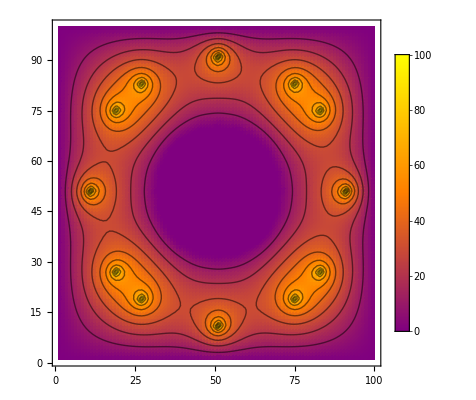

```mathematica
epilog=ListContourPlot[problem1,ContourShading->None][[1]];
ListDensityPlot[problem1,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog]
```